{m→0.504064,amp→0.499073,B→0.0620928}

{m→0.470577,amp→0.356583,B→0.0621024}

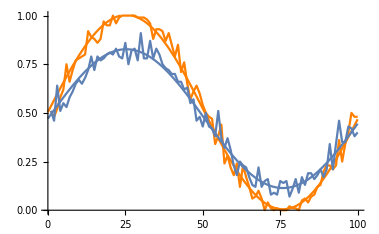

```mathematica
(* Plots a regular Ramsey sine result vs one with state destruction probability sdp. ϕ is x axis variable (0 to 2π) in numpts steps. z is the number of measurements per point. A is the default sinusoid amplitude. *)

sdp = 0.3;
ϕ = 0;
ϕ2 = 0;
z = 100;
numpts = 100;
A = 1;

sdpSine = Table[n = Total[Table[If[RandomReal[]<sdp,If[RandomReal[] < 3/4,RandomInteger[],0],Boole[RandomReal[]<1/2(1+A*Sin[ϕ])]],{i,1,z}]];
ϕ = ϕ + (2π)/numpts;
ave = n/z;
ave,{i,1,numpts}];

regSine = Table[n = Total[Table[If[RandomReal[]<0,If[RandomReal[] < 3/4,RandomInteger[],0],Boole[RandomReal[]<1/2(1+A*Sin[ϕ2])]],{i,1,z}]];
ϕ2 = ϕ2 + (2π)/numpts;
ave = n/z;
ave,{i,1,numpts}];

(* Find a curve fit and plot *)

regSineLine = FindFit[regSine, {m + amp*Sin[B p],{m<0.55,amp>0.001,B<1}}, {m,amp, B},p] 
sdpSineLine = FindFit[sdpSine, {m + amp*Sin[B p],{m<0.55,amp>0.001,B<1}}, {m,amp, B},p] 
Show[ListLinePlot[regSine, PlotRange->{0,1}, PlotStyle->Orange],Plot[m + amp*Sin[B p] /. regSineLine, {p,0,100}, PlotRange->{0,1},PlotStyle->Orange],
ListLinePlot[sdpSine, PlotRange->{0,1}],
Plot[m + amp*Sin[B p] /. sdpSineLine, {p,0,100}, PlotRange->{0,1}]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindFit::cvmit will be suppressed during this calculation.

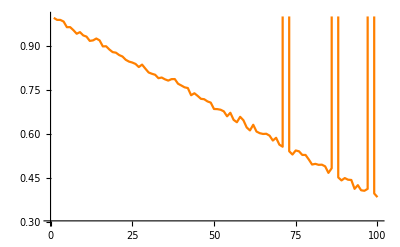

```mathematica
(* Now plotting the ratio of the sdp sine to regular sine as a function of increasing sdp, from 0 -> 1, in numptsSDP steps.*)

Clear[sdp,ϕ,ϕ2,z,A,numpts,numptsSDP,sdpSineData,regSineData,RatioData,regSineLine,sdpSineLine, a, b,m,amp,B]

sdp = 0;
ϕ = 0;
ϕ2 = 0;
z = 100;
A = 1;
numpts = 100;
numptsSDP = 100;


RatioData = Table[

sdpSineData = Table[n = Total[Table[If[RandomReal[]<sdp,If[RandomReal[] < 3/4,RandomInteger[],0],Boole[RandomReal[]<1/2(1+A*Sin[ϕ])]],{i,1,z}]];
ϕ = ϕ + (2π)/numpts;
ave = n/z;
ave,{i,1,numpts}];

regSineData = Table[n = Total[Table[If[RandomReal[]<0,If[RandomReal[] < 3/4,RandomInteger[],0],Boole[RandomReal[]<1/2(1+A*Sin[ϕ2])]],{i,1,z}]];
ϕ2 = ϕ2 + (2π)/numpts;
ave = n/z;
ave,{i,1,numpts}];

regSineLine = FindFit[regSineData, {m + amp*Sin[B p],{m<0.55,amp>0.01,B<1}}, {m,amp, B},p] ;
sdpSineLine = FindFit[sdpSineData, {m + amp*Sin[B p],{m<0.55,amp>0.01,B<1}}, {m,amp, B},p] ;


sdpMax = FindMaximum[m + amp*Sin[B p] /. sdpSineLine, p][[1]];
regMax = Max[regSineData];
ratio = sdpMax/regMax;

sdp = sdp + 1/numptsSDP;
ratio,{i,1,numptsSDP}];


Show[ ListLinePlot[{RatioData}, PlotRange->{0.3,1},PlotStyle->Orange] ]

(*line = FindFit[data1, a+ b x, {a,b},x];
Plot[a + 100 b x /. line, {x,0,1}]*)
```

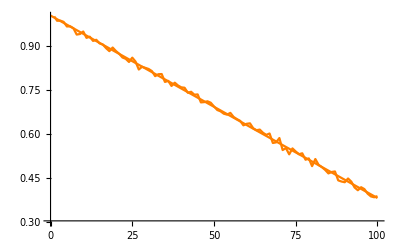

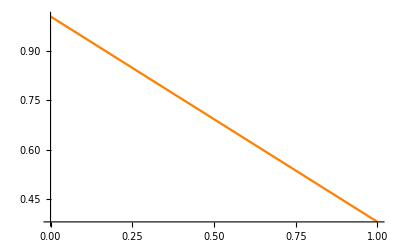

{a→1.00308,b→-0.00621717}

```mathematica
RatioDataCopy = RatioData
RatioLine = FindFit[RatioDataCopy, a+ b x, {a,b},x];

Show[
ListLinePlot[{RatioDataCopy}, PlotRange->{0.3,1},PlotStyle->Orange],
Plot[a +  b x /. RatioLine, {x,0,100},PlotStyle->Orange]
]

Plot[a +  100 b x /. RatioLine, {x,0,1},PlotStyle->Orange]

RatioLine
```

```mathematica
(* {a->1.0030777951336836,b->-0.006217172008373215} *)
```

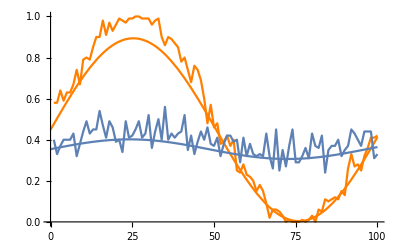

```mathematica
oamp = 0.9;
Show[ListLinePlot[regSine, PlotRange->{0,1}, PlotStyle->Orange],Plot[oamp*(m + amp*Sin[B p]) /. regSineLine, {p,0,100}, PlotRange->{0,1},PlotStyle->Orange],
ListLinePlot[sdpSine, PlotRange->{0,1}],
Plot[oamp*(m + amp*Sin[B p]) /. sdpSineLine, {p,0,100}, PlotRange->{0,1}]]
```

```mathematica
FindMaximum[oamp*(m + amp*Sin[B p]) /. sdpSineLine, p][[1]]/FindMaximum[oamp*(m + amp*Sin[B p]) /. regSineLine, p][[1]]
```

0.449601

```mathematica
FindMaximum[1*(m + amp*Sin[B p]) /. sdpSineLine, p][[1]]/FindMaximum[1*(m + amp*Sin[B p]) /. regSineLine, p][[1]]
```

0.449601